```mathematica
gamma=0.7;
delta1=0.6;
delta2=1;
U[x_,y_]:=(x^2-1)^2(x^2-delta1)+((y^2-1)^2-delta2(y-2)(y+1)^2/4)/(x^2+gamma);
Plot3D[U[x,y],{x,-1.2,1.2},{y,-1.2,1.2}]
```

-Graphics3D-

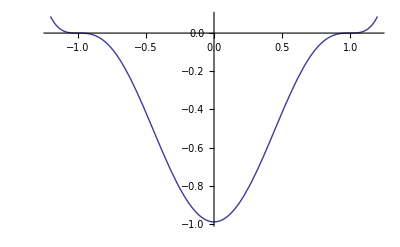

```mathematica
eps=0.99;
f[x_]:=(x^2-1)^2(x^2-eps);
Plot[f[x],{x,-1.2,1.2}]
```